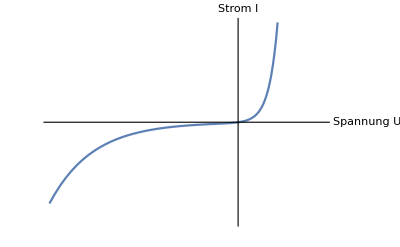

```mathematica
Id=1(100* Exp[U]-100*Exp[-0.2U]-2);
p=Plot[Id,{U,-22,10},
PlotRange->{-10000,10000},
Ticks->None,
AxesStyle->Arrowheads[0.03],
AxesLabel->{"Spannung U","Strom I"},
BaseStyle->13]
```

```mathematica
Export[NotebookDirectory[]<>"../img/diode.pdf",p]
```

/home/moritz/FP1/1002-Halbleiter/stuff/../img/diode.pdf